# Stats Practice and Data Analysis II

## Lab Ticket

Please do these problems out on a separate sheet of paper and bring them to lab with you.

1. A student measures g, the acceleration of gravity, five times, with the results (all in m/s^2): 9.9, 9.6, 9.5, 9.7, 9.8.
	a. Find her mean.
	b. Find her sample standard deviation.
	c. Find her standard deviation of the mean.

2. Three groups of particle physicists measure the mass of a certain elementary particle with the results (in units of MeV/c^2): 1.9670 ± 0.0010, 1.9690 ±0.0014, 1.9721 ± 0.0021. Find the weighted average and its uncertainty.

## 0. An example: fitting for absolute zero

Here we have pressure data for Helium obtained at temperatures between 10 and 100 degrees C. Because we aren’t working in Kelvin for which the PV=nRT form of the ideal gas law holds, we’ll have a linear relationship, but not a proportional one. We will use the data to solve for the zero temperature of the Kelvin scale. We estimate we can read our pressure gauge accurately to 200 Pa.

Temperature in degrees C and pressure in Pa:

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
T=Table[i*10,{i,1,10}];
P={23400,24400,25000,25200,26400,28000,28400,29200,30200,30800};
err = 200;
errors = Table[200,{i,1,10}];
```

First we plot our data with error bars using ErrorListPlot. Note the format it requires for the incoming data. Also note the syntax in order to print axis labels.

ErrorListPlot[{{y_1,dy_1},{y_2,dy_2},…}] plots points corresponding to a list of values y_1, y_2, …, with corresponding error bars. The errors have magnitudes dy_1,dy_2,….
ErrorListPlot[{{{x_1,y_1},ErrorBar[err_1]},{{x_2,y_2},ErrorBar[err_2]},…}] plots points with specified x and y coordinates and error magnitudes.

{{{10,23400},ErrorBar[200]},{{20,24400},ErrorBar[200]},{{30,25000},ErrorBar[200]},{{40,25200},ErrorBar[200]},{{50,26400},ErrorBar[200]},{{60,28000},ErrorBar[200]},{{70,28400},ErrorBar[200]},{{80,29200},ErrorBar[200]},{{90,30200},ErrorBar[200]},{{100,30800},ErrorBar[200]}}

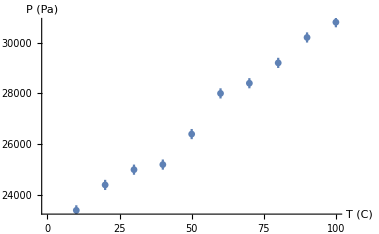

```mathematica
?ErrorListPlot
errplot=Table[{{T[[j]],P[[j]]},ErrorBar[err]},{j,1,Length[T]}]
P1=ErrorListPlot[errplot,AxesLabel->{"T (C)","P (Pa)"}]
```

Fit the data using LinearModelFit, specifying Weights -> 1/errors^2 and VarianceEstimatorFunction -> (1&) in order to force Mathmatica into treating the provided errors as experimental errors. Note that the variable ‘lm’ then contains the results from the linear model fit. The LinearModelFit function is powerful - I strongly suggest looking at the full Mathematica documentation so you get some idea of what it can do. We can plot the fit as shown in plot P2. So long as the two plots we’ve created thus far are named, we can overplot them using ‘Show’.

```mathematica
?LinearModelFit
```

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… that fits the y_i for successive x values 1, 2, ….
LinearModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… where the f_i depend on the variables x_k. 
LinearModelFit[{m,v}] constructs a linear model from the design matrix m and response vector v.

```mathematica
Table[{T[[j]],P[[j]]},{j,1,Length[T]}]
errors
lm=LinearModelFit[Table[{T[[j]],P[[j]]},{j,1,Length[T]}],x,x, Weights->1/errors^2,VarianceEstimatorFunction->(1 &)]
```

{{10,23400},{20,24400},{30,25000},{40,25200},{50,26400},{60,28000},{70,28400},{80,29200},{90,30200},{100,30800}}

{200,200,200,200,200,200,200,200,200,200}

FittedModel[22453.3+84.4848 x]

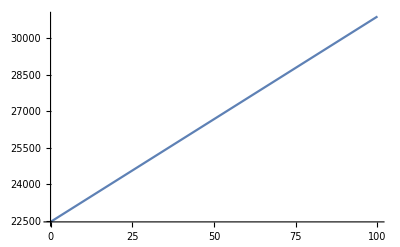

```mathematica
P2=Plot[lm[x],{x,0,100}]
```

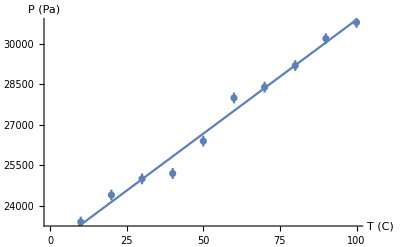

```mathematica
Show[P1,P2]
```

We can also save the best-fit parameters to a list (here ‘beta’) and have the linear model print a table summarizing the parameters fit:

```mathematica
beta = lm["BestFitParameters"]
lm["ParameterTable"]
```

{22453.3,84.4848}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 22453.3 | 136.626 | 164.342 | 2.10269×10^-15
x | 84.4848 | 2.20193 | 38.3686 | 2.3385×10^-10

At this point, since this is the first time we are using this LinearModelFit, it is appropriate to check that we understand what the function is doing. The best estimates for the slope and offset can be calculated explicitly by minimizing the χ^2 expression. The results from that minimization are presented in Taylor’s An Introduction to Error Analysis as equations 8.10-8.12. Let’s use those equations to check our answer. Here, A is the offset and B is the slope.

```mathematica
Δ=Length[T]*Total[T^2]-(Total[T])^2;
A=(Total[T^2]Total[P]-Total[T]Total[T P])/Δ//N
B=(Length[T]Total[T P]-Total[T] Total[P])/Δ//N
```

22453.3

84.4848

These two parameters are consistent - good. Taylor also presents the error propagation for A and B in equations 8.15-8.17.

```mathematica
σy=Sqrt[Total[(P-A-B T)^2]/(Length[T]-2)];
σA=σy Sqrt[Total[T^2]/Δ]//N
σB=σy Sqrt[Length[T]/Δ]//N
```

217.915

3.51202

These uncertainties are inconsistent with the standard errors presented above. This inconsistency comes from our choice of σ_y. In the LinearModelFit above, we specified that the fit should use the given weights for σ_y, rather than the calculation for σ_y performed above. If we substitute 200 Pa for σ_y in the equations for σ_A and σ_B, we should get consistent errors:

```mathematica
σA=200 Sqrt[Total[T^2]/Δ]//N
σB=200 Sqrt[Length[T]/Δ]//N
```

136.626

2.20193

Now that we understand what LinearModelFit is doing, let’s get back to the physics. Neither fit parameter is exactly what we’d like- to find absolute zero according to the Celsius scale. But we can quickly do that using these fit parameters:

```mathematica
ZeroT=-beta[[1]]/beta[[2]]
```

-265.768

That’s rather different that our expected value of -273.15. But, we need errors on ZeroT inorder to say whether our results are consistent with the expected value within the errors or not. We first obtain the errors from the linear model on both parameters and then propagate the errors on each to dZeroT.

```mathematica
dbeta=lm["ParameterErrors"]
(dbeta[[1]]/beta[[1]])
dbeta[[2]]/beta[[2]]
dZeroT=ZeroT*Sqrt[(dbeta[[1]]/beta[[1]])^2+(dbeta[[2]]/beta[[2]])^2]
```

{136.626,2.20193}

0.00608489

0.026063

-7.11297

So the range we would expect the true ZeroT to lie in given our experimental results is:

```mathematica
rangeZeroT={ZeroT+dZeroT,ZeroT-dZeroT}
```

{-272.881,-258.655}

Since the expected value for absolute zero in degrees Celsius lies is just outside this range. Recall that the errors only give where we expect the measurement to lie within 68% of the time. So this result isn’t what we’d call ‘consistent’, but it’s also reasonable to expect this sort of value to be measured given our errors and the expected value. We commonly indicate how far away from the 68% range it is by reporting the deviation in sigma (standard deviations) as per:  discrepancy/error.

```mathematica
(ZeroT +273.15)/dZeroT
```

-1.03788

We would thus call this a measurement 1.04σ away from the expected value.

## 1. Fitting Millikan’s photoelectric effect data

Frequencies are in 10^13 Hz, potentials are in volts. The relevant equation is E = e V = h f - ϕ, where e is the charge of the electron, V the voltage, h Planck’s constant, f the frequency and ϕ is related to the ‘work function’ for the specific metal used. The established value for Planck’s constant is h=4.135667 10^-15 eV s.

```mathematica
freq={54.9,69.2,74.2,82.2,96.1,118.3};
volt={-2.05,-1.50,-1.31,-0.93,-0.39,0.51};
```

1. Millikan claimed that each voltage measurement was accurate to 0.02 volt. Make an plot with error bars using ErrorListPlot. Label the axes.

```mathematica
voltErrors = Table[0.02, {i, 1, 6}]
```

{0.02,0.02,0.02,0.02,0.02,0.02}

```mathematica
voltErrPlot = Table[{{freq[[i]]*10^13, volt[[i]]},ErrorBar[voltErrors[[i]]]}, {i, 1, Length[freq]}]
```

{{{5.49×10^14,-2.05},ErrorBar[0.02]},{{6.92×10^14,-1.5},ErrorBar[0.02]},{{7.42×10^14,-1.31},ErrorBar[0.02]},{{8.22×10^14,-0.93},ErrorBar[0.02]},{{9.61×10^14,-0.39},ErrorBar[0.02]},{{1.183×10^15,0.51},ErrorBar[0.02]}}

```mathematica
voltErrorPlot = ErrorListPlot[voltErrPlot, AxesLabel-> {"Freq. (Hz.)", "Voltage (V)"}]
```

-Graphics-

2. Use LinearModelFit to fit an appropriate model to the data and create a plot that plots both this fitted model and error bar plot.

```mathematica
linearfit  = LinearModelFit[Table[{freq[[i]]*10^13, volt[[i]]}, {i, 1, 6}], x, x, Weights-> 1/voltErrors^2, VarianceEstimatorFunction->(1 &)]
```

FittedModel[-4.29675+4.06355×10^-15 x]

```mathematica
vlfplot = Plot[linearfit[x], {x, 50*10^13, 120*10^13}]
```

-Graphics-

```mathematica
Show[{vlfplot, voltErrorPlot}]
```

-Graphics-

3. Find Millikan's experimental value for Planck's constant and it's error.

The equation from above gives that e V=hf-ϕ.  Therefore, h is given by the slope of our fitted model.
h=4.06355×10^-15eV s

```mathematica
millikanBeta = linearfit["BestFitParameters"]
linearfit["ParameterTable"]
millikanDBeta = linearfit["ParameterErrors"]
(millikanDBeta[[1]]/millikanBeta[[1]])
(millikanDBeta[[2]]/millikanBeta[[2]])
```

{-4.29675,4.06355×10^-15}

| Estimate | Standard Error | t-Statistic | P-Value
1 | -4.29675 | 0.034155 | -125.801 | 2.39456×10^-8
x | 4.06355×10^-15 | 4.02078×10^-17 | 101.064 | 5.74759×10^-8

{0.034155,4.02078×10^-17}

-0.00794903

0.00989474

However, because one of the fit parameters (the slope) already describes Planck’s constant, we don’t need to do the same error propagation step in this case as in Section 0. Therefore, the expected range is

```mathematica
rangePlanck = {millikanBeta[[2]] - millikanDBeta[[2]], millikanBeta[[2]] + millikanDBeta[[2]]}
```

{4.02334×10^-15,4.10376×10^-15}

The number of standard deviations is given by

```mathematica
(millikanBeta[[2]]-4.135667 10^-15)/millikanDBeta[[2]]
```

-1.79361

Therefore, Millikan was about 2 standard deviations away from the current accepted value.

4. Extract the residuals from the fit and plot them as a function of frequency. Plots like these can be helpful to diagnose model insufficiencies, i.e. if any trend is seen in the residuals and tell us whether the initial estimated experimental errors are reasonable or not. Does there seem to be any such trend here?

```mathematica
millikanResiduals = Table[{freq[[i]]*10^13, volt[[i]] - linearfit[freq[[i]]*10^13]}, {i, 1, 6}]
```

{{5.49×10^14,0.0158625},{6.92×10^14,-0.0152251},{7.42×10^14,-0.0284026},{8.22×10^14,0.0265134},{9.61×10^14,0.00167997},{1.183×10^15,-0.00042808}}

```mathematica
ListPlot[millikanResiduals]
```

-Graphics-

There does not seem to be any kind of a trend in the residuals. However, Millikan seems to be wrong when he said all his voltage measurements were accurate to within ±0.02V—there seem to be two measurements outside that range.

5. Use the residuals from the fit to compute the sample standard deviation (i.e. the estimate of the error based on the spread in the data around the best-fit line). Remember to correct for the number of parameters fit. Compare to Millikan's claimed experimental error of 0.02 volts. Thus, what type of error might be responsible for the discrepancy between Millikan's data and the current accepted value?

The sample standard deviation is given by

```mathematica
σ = Sqrt[(1/(6-2)) Sum[(millikanResiduals[[i]][[2]])^2, {i, 1, 6}]]
```

0.0223389

This standard deviation is slightly above Millikan’s claimed error of 0.02V. The discrepancy between Millikan’s value for h and the accepted value may therefore have been due to variance in his voltage measurements, or even some small systematic error.

## 2. Classic issues in fitting a line

In 1973, statistician F. J. Anscombe published a paper, “Graphs in Statistical Analysis” which succinctly presents some major pitfalls of performing fits to data without paying more attention to what is going on. In particular, 4 data sets were presented whose linear fits are nearly identical and whose sample standard deviations in y are also nearly identical. However, inspection clearly shows that one is a good fit of the data and the other three are poor, or at least not yet well motivated fits.

Data:

```mathematica
x1={10,8,13,9,11,14,6,4,12,7,5};
y1={8.04,6.95,7.58,8.81,8.33,9.96,7.24,4.26,10.84,4.82,5.68};
data1 = Table[{x1[[i]], y1[[i]]}, {i, 1, Length[x1]}];

x2={10,8,13,9,11,14,6,4,12,7,5};
y2={9.14,8.14,8.74,8.77,9.26,8.1,6.13,3.1,9.13,7.26,4.74};
data2 = Table[{x2[[i]], y2[[i]]}, {i, 1, Length[x2]}];

x3={10,8,13,9,11,14,6,4,12,7,5};
y3={7.46,6.77,12.74,7.11,7.81,8.84,6.08,5.39,8.15,6.42,5.73};
data3 = Table[{x3[[i]], y3[[i]]}, {i, 1, Length[x3]}];

x4={8,8,8,8,8,8,8,19,8,8,8};
y4={6.58,5.76,7.71,8.84,8.47,7.04,5.25,12.5,5.56,7.91,6.89};
data4 = Table[{x4[[i]], y4[[i]]}, {i, 1, Length[x4]}];
```

1. Plot each data separately, using ListPlot.

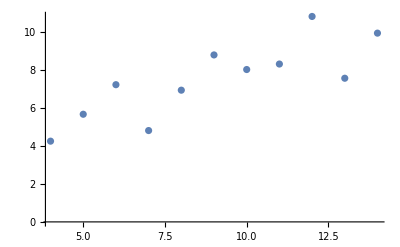

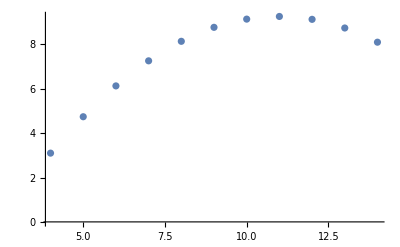

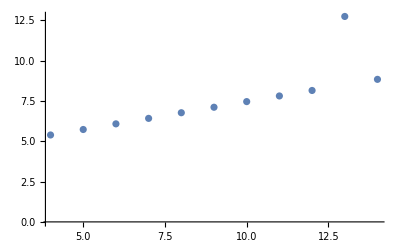

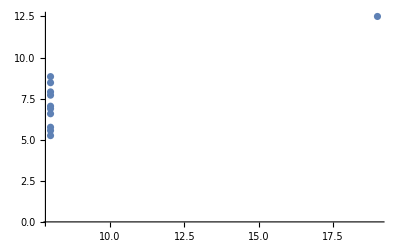

```mathematica
ListPlot[data1]
ListPlot[data2]
ListPlot[data3]
ListPlot[data4]
```

2. Perform a linear fit for each using LinearModelFit. The slope and y-intercept should be nearly identical for each data set. (Note: this time we have no experimental errors, so no need to set Weights or VarianceEstimatorFunction.)

```mathematica
lm1 = LinearModelFit[data1, x, x]
lm2 = LinearModelFit[data2, x, x]
lm3 = LinearModelFit[data3, x, x]
lm4 = LinearModelFit[data4, x, x]
```

FittedModel[3.00009+0.500091 x]

FittedModel[3.00091+0.5 x]

FittedModel[3.00245+0.499727 x]

FittedModel[3.00173+0.499909 x]

3. Overplot the results on the original data for each data set.

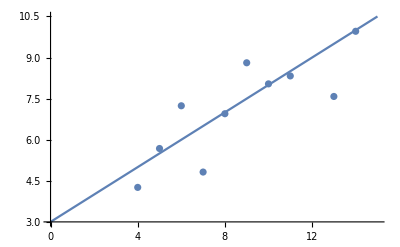

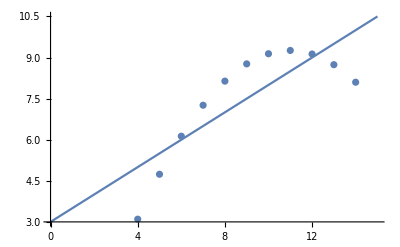

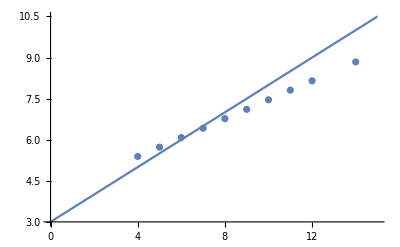

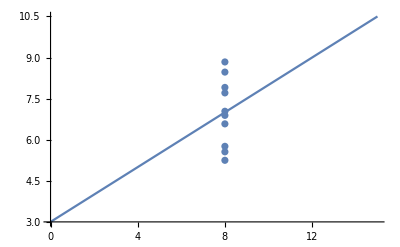

```mathematica
Show[Plot[lm1[x], {x, 0, 15}], ListPlot[data1]]
Show[Plot[lm2[x], {x, 0, 15}], ListPlot[data2]]
Show[Plot[lm3[x], {x, 0, 15}], ListPlot[data3]]
Show[Plot[lm4[x], {x, 0, 15}], ListPlot[data4]]
```

4. Determine an estimate of the sample standard deviation in the y-direction from the residuals for each data set. (Again, remember to correct for the number of parameters fit.)

The residual plots are:

```mathematica
resid1 = Table[data1[[i]][[2]] - lm1[data1[[i]][[1]]], {i, 1, Length[data1]}];
resid2 = Table[data2[[i]][[2]] - lm2[data2[[i]][[1]]], {i, 1, Length[data2]}];
resid3 = Table[data3[[i]][[2]] - lm3[data3[[i]][[1]]], {i, 1, Length[data3]}];
resid4 = Table[data4[[i]][[2]] - lm4[data4[[i]][[1]]], {i, 1, Length[data4]}];
```

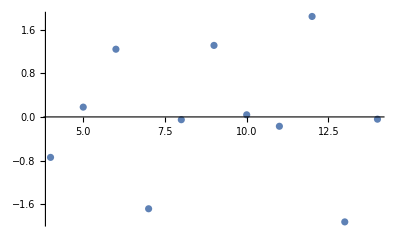

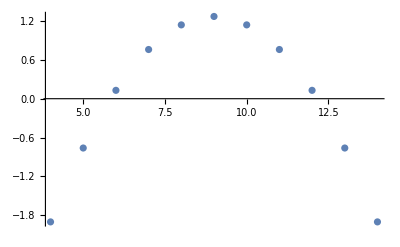

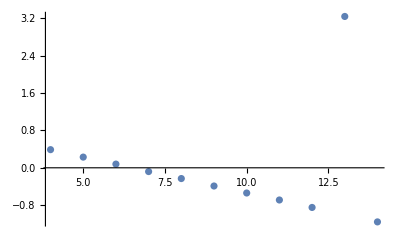

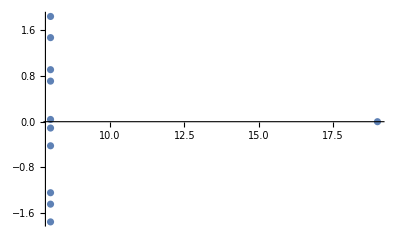

```mathematica
ListPlot[Table[{data1[[i]][[1]], resid1[[i]]}, {i, 1, Length[data1]}]]
ListPlot[Table[{data2[[i]][[1]], resid2[[i]]}, {i, 1, Length[data2]}]]
ListPlot[Table[{data3[[i]][[1]], resid3[[i]]}, {i, 1, Length[data3]}]]
ListPlot[Table[{data4[[i]][[1]], resid4[[i]]}, {i, 1, Length[data4]}]]
```

Then the standard deviations are

```mathematica
σ1 = Sqrt[1/(Length[x1]-2) Sum[resid1[[i]]^2, {i, 1, Length[resid1]}]]
σ2 = Sqrt[1/(Length[x2]-2) Sum[resid2[[i]]^2, {i, 1, Length[resid2]}]]
σ3 = Sqrt[1/(Length[x3]-2) Sum[resid3[[i]]^2, {i, 1, Length[resid3]}]]
σ4 = Sqrt[1/(Length[x4]-2) Sum[resid4[[i]]^2, {i, 1, Length[resid4]}]]
```

1.2366

1.23721

1.23631

1.2357

5. We, as humans can more or less *see* what is going wrong with fitting to each of these distributions. Consider potential quanitative ways to distinguish between these fits. Try one or two of these ideas and discuss the ideas and results with a classmate, the TA, or the instructor.


By squaring the residuals, outliers are caught more easily. This still doesn’t do much to catch the quadratic or the clustered data.

```mathematica
lmrf1 = LinearModelFit[Table[{data1[[i]][[1]], resid1[[i]]^2}, {i, 1, Length[data4]}], x, x]
lmrf2 = LinearModelFit[Table[{data2[[i]][[1]], resid2[[i]]^2}, {i, 1, Length[data4]}], x, x]
lmrf3 = LinearModelFit[Table[{data3[[i]][[1]], resid3[[i]]^2}, {i, 1, Length[data4]}], x, x]
lmrf4 = LinearModelFit[Table[{data4[[i]][[1]], resid4[[i]]^2}, {i, 1, Length[data4]}], x, x]
```

FittedModel[0.281852+0.1077 x]

FittedModel[1.25239-3.37097×10^-16 x]

FittedModel[-2.92925+0.464424 x]

FittedModel[2.3737-0.124932 x]

```mathematica
lmrf1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.281852 | 1.36067 | 0.207143 | 0.840509
x | 0.1077 | 0.142637 | 0.755066 | 0.469507

```mathematica
lmrf2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.25239 | 1.21866 | 1.02767 | 0.330929
x | -3.37097×10^-16 | 0.127751 | -2.63871×10^-15 | 1

```mathematica
lmrf3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.92925 | 2.57444 | -1.13782 | 0.284578
x | 0.464424 | 0.269874 | 1.72089 | 0.119379

```mathematica
lmrf4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.3737 | 1.14487 | 2.07334 | 0.0679953
x | -0.124932 | 0.120015 | -1.04097 | 0.325046

We can catch the example where nearly all the points are clustered on the x-axis by comparing the mean and median of a set of data

```mathematica
Mean[x1] - Median[x1]
```

0

```mathematica
Mean[x2] - Median[x2]
```

0

```mathematica
Mean[x3] - Median[x3]
```

0

```mathematica
Mean[x4] - Median[x4]
```

1

We can also do the same thing for the y - axis to figure out when a linear fit may not be appropriate:

```mathematica
Mean[y1]-Median[y1]
```

-0.0790909

```mathematica
Mean[y2]-Median[y2]
```

-0.639091

```mathematica
Mean[y3]-Median[y3]
```

0.39

```mathematica
Mean[y4]-Median[y4]
```

0.460909

In both of these cases, the good fit (data set 1) had a small difference between the mean and median. The second test, especially, was able to detect all three bad fits. However, I can still think of an example (like a cubic S-curve) that would return a low value for that test, but which are not linear.

## 3. Fitting Geiger and Marsden’s Rutherford scattering data

Angle of detector, in degrees, and number of scintillations observed:

```mathematica
angle={150,135,120,105,75,60,45,37.5,30,22.5,15};
number={22.2,27.4,33.0,47.3,136,320,989,1760,5260,20300,105400};
```

1. Make a plot of the above data. Which data belongs on which axis? Use a logarithmic scale for the y-axis. [Either use ListLogPlot or ListLogLinearPlot depending if you want y or x axis to be logarithmic, respectively.] Label your axes.

```mathematica
geigerData = Table[{angle[[i]], number[[i]]}, {i, 1, Length[angle]}]
```

{{150,22.2},{135,27.4},{120,33.},{105,47.3},{75,136},{60,320},{45,989},{37.5,1760},{30,5260},{22.5,20300},{15,105400}}

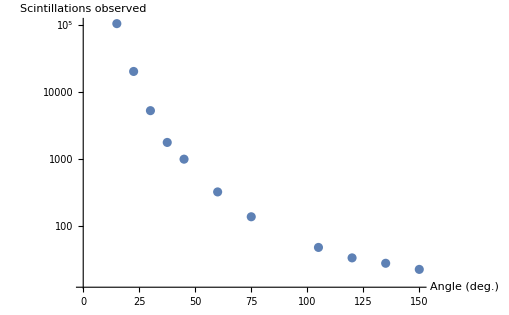

```mathematica
geigerPlot = ListLogPlot[geigerData, AxesLabel->{"Angle (deg.)", "Scintillations observed"}]
```

2.  In addition to other errors that may be present, count data like this follows the Poisson distribution and has what are called "Poisson errors". Poisson errors are nearly Gaussian, except at low counts. That sounds good, however, the standard deviation of the approximate Gaussian goes like the square root of the number of counts, so we should account for that when supplying errors.

```mathematica
counterrors = Table[Sqrt[number[[i]]], {i, 1, Length[number]}];
```

```mathematica
geigerErrors = Table[{geigerData[[i]], ErrorBar[counterrors[[i]]]}, {i, 1, Length[angle]}];
```

3. Use NonlinearModelFit to find the best fit. The functional form should be f[θ]=A/Sin[θ/2]^4. [This is a model that is linear in the parameters, here we are just practicing using NonlinearModelFit. We would have to pull one trick to make this function work in LinearModelFit: set IncludeConstantBasis -> False, in order to have it avoid fitting it’s default constant additive offset.] Remember to use your errors from 2 using Weights and VarianceEstimatorFunction.

```mathematica
nlfmGeiger = NonlinearModelFit[geigerData, aaa/Sin[(theta Degree)/2]^4, {aaa},theta, Weights->1/counterrors^2, VarianceEstimatorFunction->(1 &)]
```

FittedModel[29.3579 Csc[(° theta)/2]^4]

4. Plot the fit over the data with a logarithmic y-axis. Where does it fit well versus poorly? Inspect the residuals as a function of angle and try plotting the errors on this plot. Why does the fit look the way it does?

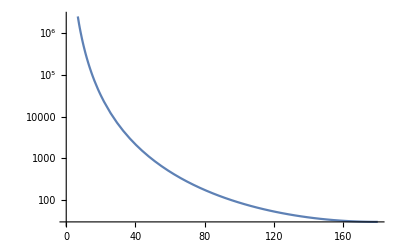

```mathematica
geigerfitplot = LogPlot[nlfmGeiger[thet], {thet, 0, 180}]
```

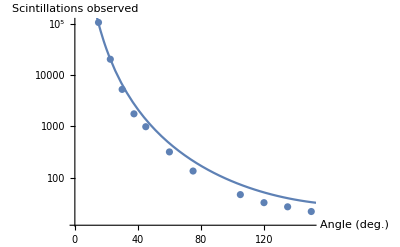

```mathematica
Show[geigerPlot, geigerfitplot]
```

This fit is best at lower angles, and starts to drift at larger angles.

```mathematica
geigerResids = Table[{angle[[i]], number[[i]] - nlfmGeiger[angle[[i]]]}, {i, 1, Length[angle]}]
```

{{150,-11.5249},{135,-12.8962},{120,-19.1919},{105,-26.8069},{75,-77.7651},{60,-149.727},{45,-379.884},{37.5,-989.974},{30,-1282.45},{22.5,33.3283},{15,4257.27}}

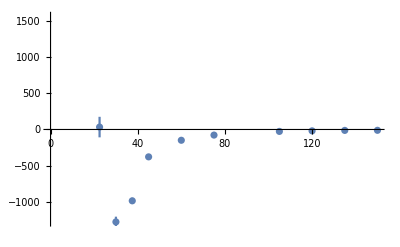

```mathematica
ErrorListPlot[Table[{geigerResids[[i]], ErrorBar[counterrors[[i]]]}, {i, 1, Length[angle]}]]
```

It looks like the point at 22.5 is a bit of an outlier, which is skewing the rest of the model. If this point were removed, there is a clear exponential decay that could be accounted for in the model.